2.1 Index of fixed point

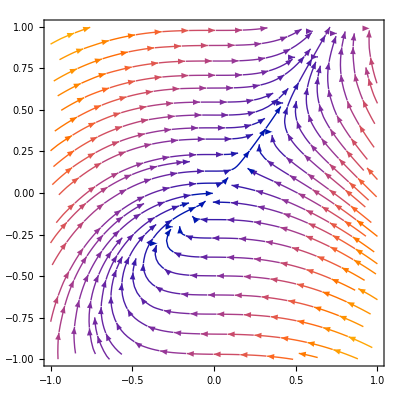

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y-x;
ydot = x^2;
P ={xdot,ydot};
lim = 1;
StreamPlot[P,{ x,-lim,lim},{y,-lim,lim}]
```

b)

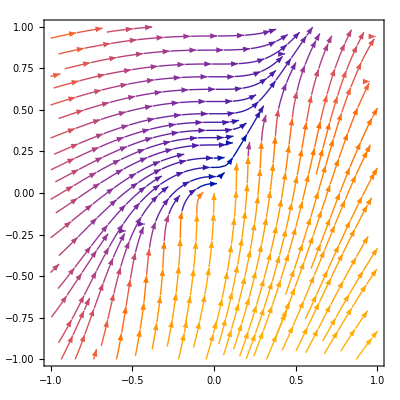

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y-x;
ydot = x^2;
P ={xdot,ydot};
rdot = x()
```

c)

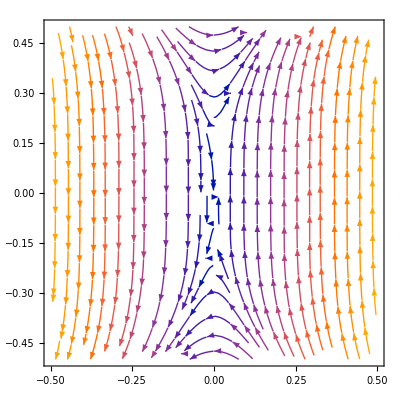

```mathematica
xdot =.;ydot=.;y=.;x=.;P=.;lim=.;
xdot = y^3;
ydot = x;
P ={xdot,ydot};
lim = 0.5;
StreamPlot[P,{ x,-lim,lim},{y,-lim,lim}]
```

2.2

```mathematica
xdot=.;ydot=.;y=.;x=.;sigma=.;
xdot = y;
ydot = -Sin[x]-sigma y
Dsolve[xdot,ydot]
```

-sigma y-Sin[x]

Dsolve[y,-sigma y-Sin[x]]

2.3

```mathematica
xdot=.;ydot=.;y=.;x=.;sigma=.;mu=.;
xdot = mu x - 5 y -x^3;
ydot = 5x+mu y+3y^3;
```